## 3.029 Spring 2022 Lecture 04 - 02/09/2022

## Liquid - Gas Phase Transitions

In 3.020, you have probably covered thermodynamic state variables such as pressure, , temperature, , and the system’s volume,

Equations of state are thermodynamic relations which relate these thermodynamic variables, and thus describe the state of a system under these physical conditions

They take the general form:

One simple such equation of state, pertaining to non-interacting particles, is called the ideal gas law and is given by:

where  is the number of moles of a substance

and  is the ideal gas constant

WolframAlphaQueryParseResults

207861565453831/25000000000000 J/(K mol)

The equation’s simplicity permits thermodynamic development without long and tedious equations.

The ideal gas law, however, has assumptions that are too simple to capture the behavior of real systems.  Those assumptions are:

Gas molecules are treated as point particles (occupying no volume)

Gas molecules are allowed to interact with their container, but not one another

## Van der Waals Gas

Replacing these with less simple assumptions gives rise to rich phenomena, and in particular phase transitions.

Johannes Van der Waals proposed a modified equation of state in his thesis which is now known as the Van der Waals equation.

where  is the molar volume

and  and  are constants relating to molecular interactions and volumes

it’s easy to see that if both  and  are zero, the van der Waals equation reduces to the ideal gas law

```mathematica
vdWEquationOfState[a_,b_,r_][pressure_,molarVolume_,temperature_]=(pressure+a/molarVolume^2)(molarVolume-b)==r temperature;
```

### Critical Behaviour

Later in 3.020, you will define various thermodynamic relations (Maxwell’s relations)

and bounds their stability set to materials properties

One of these relations, called the isothermal bulk modulus , relates the change in the pressure of material following a change in its volume at fixed temperature

In stable materials, pressure decreases with increased volume and thus the isothermal bulk modulus is positive.  The reasoning goes as follows:

If the bulk modulus becomes negative, then a decrease in volume would be resisted by decreasing pressure and the volume would continue to shrink until it goes to zero (or the bulk modulus becomes positive).

Thus a negative isothermal bulk modules would produce spontaneous volume changes — i.e. a phase transition.

Mathematically, we can express this stability condition as

which highlights that in order for the system to be stable, pressure must decrease with increasing volume.

For a gas obeying the van der Waals equation of state, there exists a critical temperature, T_c, above which eq. (5) is always satisfied – highlighting the stable region.

In order to find T_c, the conditions for a negative slope in pressure versus molar volume need to be worked out. As such, we rearrange (3) for pressure:

```mathematica
vdWEquationOfStatePressure[a_,b_,r_][molarVolume_,temperature_]=pressure/.First[Solve[vdWEquationOfState[a,b,r][pressure,molarVolume,temperature],pressure]]
```

(-a b+a molarVolume-molarVolume^2 r temperature)/((b-molarVolume) molarVolume^2)

We require that the molar volume exhibits an inflection point

This amounts to the first and second derivatives (w.r.t. molar volume) vanish

```mathematica
extremumEquation=Simplify[
Derivative[1,0][vdWEquationOfStatePressure[a,b,r]][vCritical,tCritical]==0
]
```

(2 a (b-vCritical)^2-r tCritical vCritical^3)/((b-vCritical) vCritical)==0

```mathematica
inflectionEquation=Simplify[
Derivative[2,0][vdWEquationOfStatePressure[a,b,r]][vCritical,tCritical]==0
]
```

(3 a (b-vCritical)^3+r tCritical vCritical^4)/((b-vCritical) vCritical)==0

Coding comment: The derivatives above were evaluated using the Derivative operator. This is referred to as functional differentiation, and we often find it to be the most natural choice in functional programming (e.g. when manipulating mathematical expressions).

An alternative is to use partial derivatives notation, which instead acts on expressions and is given by the D function in Mathematica. The examples below are provided in hope of demystifying the differences and similarities between the two.

```mathematica
myFunction[univariateArgument_]:=4 univariateArgument^3
functionalDerivative=Derivative[1][myFunction]

functionalDerivative[x]
functionalDerivative[3]
```

12 #1^2&

12 x^2

108

Solving our two equations for the constants a & b

```mathematica
criticalSolutionsSubstitutions=Solve[{extremumEquation,inflectionEquation},{a,b}][[1]]
```

{a→(9 r tCritical vCritical)/8,b→vCritical/3}

We can express the van der Waals equation of state at the critical point as:

```mathematica
vdWEquationOfStateCritical[r_][pCritical_,vCritical_,tCritical_]=vdWEquationOfState[(9 r tCritical vCritical)/8,vCritical/3,r][pCritical,vCritical,tCritical]
```

2/3 (pCritical+(9 r tCritical)/(8 vCritical)) vCritical==r tCritical

In this form, the equation can be solved for any of the critical variables in terms of the other two.

```mathematica
criticalVolume=vCritical/.Solve[vdWEquationOfStateCritical[r][pCritical,vCritical,tCritical], vCritical][[1]]
```

(3 r tCritical)/(8 pCritical)

```mathematica
criticalPressure=pCritical/.Solve[vdWEquationOfStateCritical[r][pCritical,vCritical,tCritical], pCritical][[1]]
```

(3 r tCritical)/(8 vCritical)

```mathematica
criticalTemperature=tCritical/.Solve[vdWEquationOfStateCritical[r][pCritical,vCritical,tCritical], tCritical][[1]]
```

(8 pCritical vCritical)/(3 r)

Using these we can define the following dimensionless ratio:

### Non-dimensional form

Using these critical points, we can define new non-dimensional variables, so that we can plot the behavior as deviations away from criticality.

We’ll define the following three normalized variables

```mathematica
pNormalvdWEquationOfStateNormalized[vNormalized_,tNormalized_]=pNormalized/.Solve[vdWEquationOfState[(9 r tCritical vCritical)/8,vCritical/3,r][pNormalized criticalPressure,vNormalized vCritical,tNormalized tCritical],pNormalized][[1]]
```

(3-9 vNormalized+8 tNormalized vNormalized^2)/(vNormalized^2 (-1+3 vNormalized))

And plot various normalized isotherms

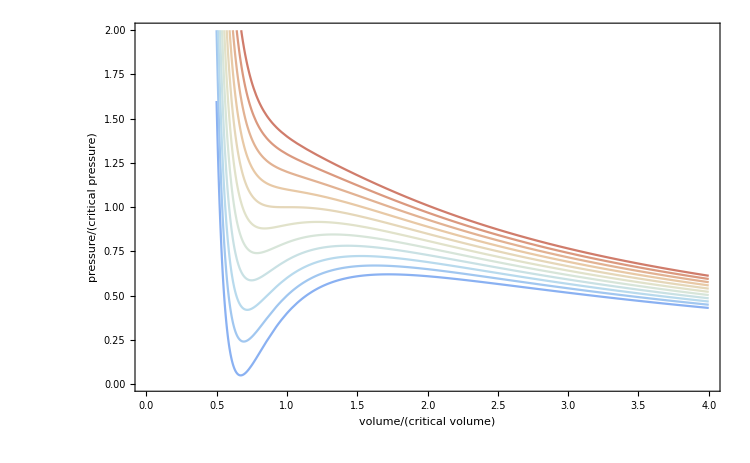

```mathematica
isothermPlot=With[ {curves = Table[pNormalvdWEquationOfStateNormalized[vNormalized,tNormalized],{tNormalized,0.85,1.1,0.025}]},
Plot[curves,{vNormalized,0.5,4}, ]
]
```

### Instability

Regions of positive slope identify where the system is mechanically unstable

Let’s visualize this unstable region by plotting where the second derivative changes sign (the spinodal points)

There is always one spinodal point separating local maxima from minima.

We use our solution to eliminate the normalized temperature

```mathematica
normalizedTemperatureSubstitution=Solve[pNormalvdWEquationOfStateNormalized[vNormalized,tNormalized]==pNormalized,tNormalized][[1]]
```

{tNormalized→((-1+3 vNormalized) (3+pNormalized vNormalized^2))/(8 vNormalized^2)}

and recall our definition of the bulk modulus:

```mathematica
bulkModulus[vNormalized_,pNormalized_]=Simplify[-vNormalized Derivative[1,0][pNormalvdWEquationOfStateNormalized][vNormalized,tNormalized]/.normalizedTemperatureSubstitution]
```

(3 (2-3 vNormalized+pNormalized vNormalized^3))/(vNormalized^2 (-1+3 vNormalized))

To define the spinodal region as the volumes this crosses the zero point

```mathematica
spinode[vNormalized_]=pNormalized/.Solve[bulkModulus[vNormalized,pNormalized]==0,pNormalized][[1]]
```

(-2+3 vNormalized)/vNormalized^3

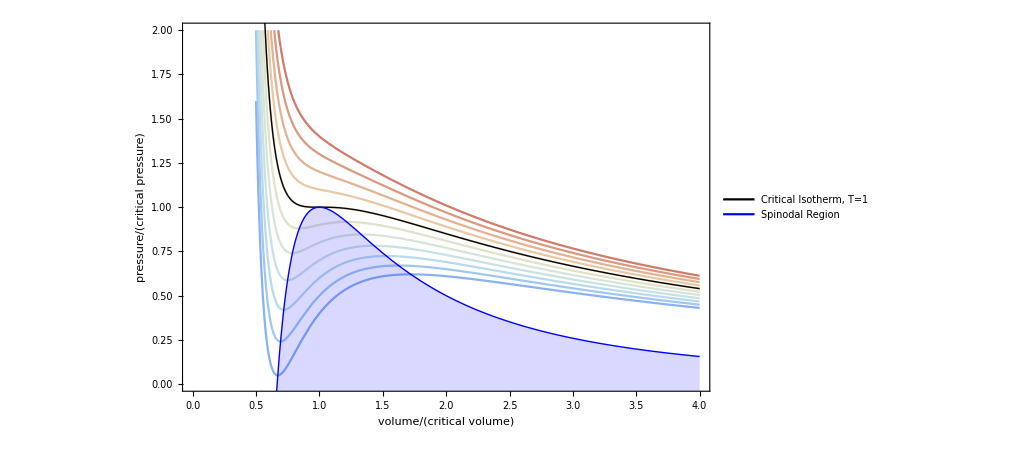

```mathematica
Show[isothermPlot,Plot[{pNormalvdWEquationOfStateNormalized[vNormalized,1],spinode[vNormalized]},{vNormalized,0.5,4},]]
```

### Compressibility

The isothermal compressibility is related to the inverse of the isothermal bulk modulus:

This is an example of a susceptibility function, i.e. the measure of change of an extensive property upon variation of an intensive property.

It’s often convenient to work with susceptibilities when possible for two reasons:

They can be experimentally measured

They diverge at phase transitions

```mathematica
compressibility[vNormalized_,tNormalized_]=Simplify[-1/vNormalized/Derivative[1,0][pNormalvdWEquationOfStateNormalized][vNormalized,tNormalized]]
```

((1-3 vNormalized)^2 vNormalized^2)/(6 (-1+6 vNormalized-9 vNormalized^2+4 tNormalized vNormalized^3))

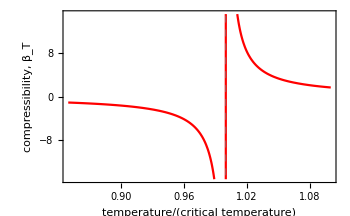
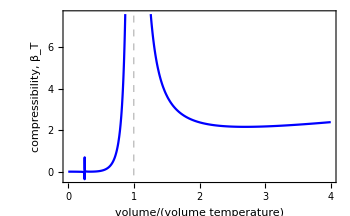

```mathematica
Row[{
Plot[compressibility[1,tNormalized],{tNormalized,0.85,1.1},],
Plot[compressibility[vNormalized,1],{vNormalized,0,4},]}]
```

As expected, the compressibility diverges around the critical point